# On-chip MBQC machines of NV-center

```mathematica
Environment["MOSEKLM_LICENSE_FILE"]
```

:/home/cica/mosek/mosek.lic

## VQD setup

Set the main directory as the current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink package
One may also use the off-line questlink.m file, change it to the location of the local file

```mathematica
Quiet@Import["https://qtechtheory.org/questlink.m"]
```

This will download a binary file  quest_link from the repo; some error will show if the system tries to override the file
Use CreateLocalQuESTEnv[quest_link_file] if the binary has already exists

```mathematica
(*CreateDownloadedQuESTEnv[];*)
CreateLocalQuESTEnv["quest_link"];
```

Load the VQD package; must be loaded after QuESTlink is loaded

```mathematica
(*Import["https://raw.githubusercontent.com/QTechTheory/VQD/refs/heads/master/vqd.wl"]*)
Import["~/VQD/vqd.wl"]
```

## Native gates

Direct iIitialisation and measurement are on the NV electron spin only
Init_0, M_0
Single-qubit gates
Rx_q[θ], Ry_q[θ], Rz_q[θ] 
Two-qubit gates are conditional rotation, where  CRσ[θ]:=|0X0|⊗ Rσ[θ]+|1X1|⊗ Rσ[-θ]
CRx_(0,q)[θ], CRy_(0,q)[θ]
others: doing nothing
Wait_q[duration]

## User device configuration

Qubit 0 indicates electron spin,and the rest are nuclear spins  C^13 and N^14 - if applicable
Time unit is second (s)
Frequency unit is  Hertz (Hz)

In the following example, we have a 4-qubit system. Q0 -> Electronic spin qubit and the rest are Nuclear spin qubits

```mathematica
Options[NVCenterDelft]={
QubitNum->4,
(* T1 of each qubit *)
T1-> <|0-> 3600,1->60,2->60,3->60 |>,
(* T2 of each qubit; we assume dynamical decoupling is actively applied *)
T2-> <|0-> 1.5,1->10,2->10,3->10|>,
(* dipolar interaction among nuclear spins: cross-talk ZZ-coupling in order of a few Hz on passive noise *)
FreqWeakZZ->5,
(* direct single rotation on Nuclear spin is done via RF, put electron in state -1 leave out the Rx Ry on nuclear spins ideally. *)
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500|>,
(* usually done virtually *)
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3|>,
(* Frequency of CRot gate, conditional rotation done via dynamical decoupling or dd+RF. The gate is conditioned on electron spin state *)
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3|>,
(* Fidelity of CRot gate  *)
FidCRot-><|1-> 0.98,2->0.98, 3->0.98|>,
(* fidelity of x- and y- rotations on each qubit *)
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99|>,
(* fidelity of z- rotations on each qubit *)
FidSingleZ->  <| 0->0.9999,1-> 0.9999,2->0.99999, 3->0.9999 |>,
(* Error ratio of 1-qubit depolarising:dephasing of x- and y- rotations  *)
EFSingleXY->{0.75,0.25},
(* Error ratio of 2-qubit depolarising:dephasing of CRot gate *)
EFCRot->{0.9,0.1},
(* initialization fidelity on the electron spin *)
FidInit-> 0.999,
(* initialization duration on the electron spin *)
DurInit->2*10^-3,
(* measurement fidelity on the electron spin *)
FidMeas->0.946,
(* measurement duration on the electron spin *)
DurMeas->2*10^-5,
(* Switch to standard passive noise *)
StdPassiveNoise -> True
};
```

-Graphics-

```mathematica
NVDevice=NVCenterDelft[];
```

```mathematica
NVNoise=<|"description"->"On Chip NVCenter with explicit electronic spin"|>;
```

## QuESTlink and convention

QuEST uses Least Significant Bit
QuEST uses Superopeator to store and perform operation on density matrices

By LSB, therefore:
Column-stacking:  A_(i,j)|i X j| :> A_(i,j)j i : { 00, 10, 01, (11})_(q0, q1),  in QuEST: {00,01,10,11}_(q1,q0)
Row-stacking: A_(i,j)|i X j| :> A_(i,j)i j: {00, 01, 10, (11})_(q0,q1), in QuEST: {00,10,01,11}_(q1,q0)

## Noise channel optimisation

```mathematica
ClearAll[hermitianTemplate]
hermitianTemplate::usage="hermitianTemplate[dim, variable(or {diag, real, imag}), [init_matrix]]. 
Create template for hermitian matrix. Returns {hermitian template, elements, elements_constraints, initial values} with initial value as unnormalized bell state |00>+|11>. Note that the resulting hermitian operator is in choi form.";
hermitianTemplate[n_, var_List] := Module[{d, a, z, superop, elemconst, initval, elems},
	{d, a, z} = var;
	(* symbolic superoperator *)
	superop = DiagonalMatrix[Array[Subscript[d, #,#]&, {n}]];
	Table[
		superop[[r, c]] = Subscript[a, r,c] + ⅈ Subscript[z, r,c];
		superop[[c, r]] = Subscript[a, r,c] - ⅈ Subscript[z, r,c]
		,{r, n}, {c, r+1, n}];
		
	(* elements *)
	elems = Flatten @ {Table[Subscript[d, i,i] ∈ Reals, {i, n}],
				Table[{Subscript[a, r,c] ∈ Reals, Subscript[z, r,c]  ∈ Reals}, {r, n}, {c, r + 1, n}]};
	
	(* constraint on each element *)
	elemconst = Flatten[
		{ 
		(* diagonal constraint is probability value *)
		(0 <= Subscript[d, #,#] <= 1)& /@ Range[n], 
		(* off-diagonal constraint is complex disk with radius 1 *)
		Table[Table[
			Sqrt[Subscript[a, row, col]^2 + Subscript[z, row, col]^2] <= 1
			, {col, row + 1, n}], {row, n}]
		}
		];
	(* initial value as an identity matrix *)
	initval = Association @ Flatten[
		{ 
		Subscript[d, #, #] -> 0 &  /@ Range[n], 
		Table[Table[Subscript[a, row, col] -> 0, {col, row + 1, n}], {row, n}],
		Table[Table[Subscript[z, row, col] -> 0, {col, row + 1, n}], {row, n}]
		}
		];
	initval[Subscript[d, 1,1]]=1;
	initval[Subscript[d, 4,4]]=1;
	initval[Subscript[a, 1,4]]=1;
	{superop, elems, elemconst, Normal @ initval}		
]
```

## Preparation operation

XY-plane basis: +_θ= {1/(√2),ⅇ^(ⅈ θ)/(√2)} and -_θ={1/(√2),-ⅇ^(ⅈ θ)/(√2)}
 Note that, NV center has star connectivity . Initialisation of the qubit happens on the center qubit (electron spin qubit) . See “Native Gates” section
 My strategy here is prepare the state in the center, then perform partial SWAP to the edge qubits (Nuclear spin qubits).
 Here we do not need the full swap because the states are rebits (Real qubits)

```mathematica
xyDensityMatrix::usage="xyDensityMatrix[θ]. Create rebit in XY plane with parameter θ";
xyDensityMatrix[θ_]:=KroneckerProduct[{1/(√2),ⅇ^(ⅈ θ)/(√2)},{1/(√2),ⅇ^(-ⅈ θ)/(√2)}]
```

In vector simulation, the state can be obtained by two single rotations. The following operations show the ideal case should be able to prepare any XY-state
This direct operation can be done on the electronic spin

```mathematica
mat = CalcCircuitMatrix[{Subscript[Ry, 0][π/2],Subscript[Rz, 0][θ]}]
```

{{ⅇ^(-(ⅈ θ)/2)/(√2),-ⅇ^(-(ⅈ θ)/2)/(√2)},{ⅇ^((ⅈ θ)/2)/(√2),ⅇ^((ⅈ θ)/2)/(√2)}}

```mathematica
(* State +θ*)
ⅇ^(ⅈ θ/2)*mat.{1,0}
```

{1/(√2),ⅇ^(ⅈ θ)/(√2)}

```mathematica
(* State -θ*)
-ⅇ^(ⅈ θ/2)*mat.{0,1}
```

{1/(√2),-ⅇ^(ⅈ θ)/(√2)}

### Prepare XY - state on the electron spin

```mathematica
xyElectron[θ_]:=Sequence@@{Subscript[Init, 0],Subscript[Ry, 0][π/2],Subscript[Rz, 0][θ]}
```

```mathematica
Flatten[{xyElectron[θ]}/.NVDevice[Aliases]]
supop1=CalcCircuitMatrix@%
```

{Damp_0[1.],Ry_0[π/2],Rz_0[θ]}

{{0.5,0.,0.,0.5},{0.+0.5 ⅇ^(ⅈ θ),0.,0.,0.+0.5 ⅇ^(ⅈ θ)},{0.+0.5 ⅇ^(-ⅈ θ),0.,0.,0.+0.5 ⅇ^(-ⅈ θ)},{0.5,0.,0.,0.5}}

Density matrix test: Start with an arbirary random mix density matrix  and see if the electron spin is initialised to the XY-plane states

```mathematica
ρmat1=RandomMixState@1
```

{{0.797908,0.00564788+0.0804319 ⅈ},{0.00564788-0.0804319 ⅈ,0.202092}}

```mathematica
(* Superoperate *)
Chop@SuperOperate[ρmat1, supop1]
(* compare to the GOAL*)
Chop@N@xyDensityMatrix@θ
```

{{0.5,0.5 ⅇ^(ⅈ θ)},{0.5 ⅇ^(-ⅈ θ),0.5}}

{{0.5,0.5 2.71828^((0.-1. ⅈ) θ)},{0.5 2.71828^((0.+1. ⅈ) θ),0.5}}

### Prepare XY - state on the nuclear spin

```mathematica
Subscript[xyNuclear, q_/;q>0][θ_]:=Sequence@@{Subscript[Init, 0],Subscript[Ry, 0][π/2],Subscript[CRx, 0,q][π/2],Subscript[Rx, 0][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Ry, q][π/2],Subscript[Rz, q][θ]}
```

```mathematica
Flatten[{Subscript[xyNuclear, 1][θ]}/.NVDevice[Aliases]]
supop2=CalcCircuitMatrix@%;
```

{Damp_0[1.],Ry_0[π/2],U_(0,1)[{{1/(√2),0,-ⅈ/(√2),0},{0,1/(√2),0,ⅈ/(√2)},{-ⅈ/(√2),0,1/(√2),0},{0,ⅈ/(√2),0,1/(√2)}}],Rx_0[π/2],U_(0,1)[{{1/(√2),0,1/(√2),0},{0,1/(√2),0,-1/(√2)},{-1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)}}],Ry_1[π/2],Rz_1[θ]}

Density matrix test: Start with an arbirary random mix density matrix  and see if the nuclear spin is initialised to the XY-plane states

```mathematica
ρmat2=RandomMixState@2
```

{{0.455628,0.0240054-0.00756958 ⅈ,0.228449-0.241013 ⅈ,-0.143947+0.0899647 ⅈ},{0.0240054+0.00756958 ⅈ,0.102571,-0.0288114-0.0682436 ⅈ,0.0461216+0.0399107 ⅈ},{0.228449+0.241013 ⅈ,-0.0288114+0.0682436 ⅈ,0.330751,-0.169711-0.0246818 ⅈ},{-0.143947-0.0899647 ⅈ,0.0461216-0.0399107 ⅈ,-0.169711+0.0246818 ⅈ,0.111049}}

```mathematica
(* Superoperate, then trace the electron spin *)
PartialTrace[Chop@SuperOperate[ρmat2, supop2],0]
(* compare to the GOAL*)
xyDensityMatrix@θ
```

{{0.5,0.5 ⅇ^(ⅈ θ)},{0.5 ⅇ^(-ⅈ θ),0.5}}

{{1/2,ⅇ^(-ⅈ θ)/2},{ⅇ^(ⅈ θ)/2,1/2}}

## FULL NOISE: preparation

### Noisy preparation of the electron spin to state +θ

```mathematica
elprep={xyElectron[θ]}
```

{Init_0,Ry_0[π/2],Rz_0[θ]}

Note that here is only preparing the electronic spin state to XY plane. Notice the presence of Cross-talk are forming all-to-all connectivity

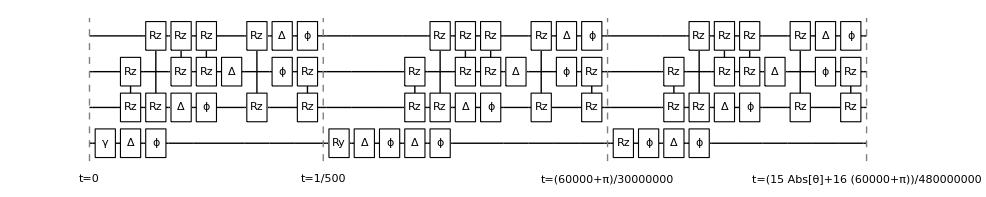

```mathematica
elprepNoisy=Assuming[Element[θ,Reals],Simplify@InsertCircuitNoise[elprep,NVDevice,ReplaceAliases->True]];
DrawCircuit@%
```

```mathematica
elprepNoisy/.θ->π
```

{{0,{Damp_0[0.999]},{Depol_0[0.],Deph_0[0.],R[0,Z_1 Z_2],R[0,Z_1 Z_3],R[0,Z_2 Z_3],Depol_1[0.0000249996],Deph_1[0.00009999],R[1/2500,Z_2 Z_3],Depol_2[0.0000249996],Deph_2[0.00009999],R[1/2500,Z_1 Z_3],Depol_3[0.0000249996],Deph_3[0.00009999],R[1/2500,Z_1 Z_2]}},{1/500,{Ry_0[π/2],Depol_0[0.000281303],Deph_0[0.0000937676]},{Depol_0[0.],Deph_0[0.],R[0,Z_1 Z_2],R[0,Z_1 Z_3],R[0,Z_2 Z_3],Depol_1[1.309×10^-9],Deph_1[5.23599×10^-9],R[π/150000000,Z_2 Z_3],Depol_2[1.309×10^-9],Deph_2[5.23599×10^-9],R[π/150000000,Z_1 Z_3],Depol_3[1.309×10^-9],Deph_3[5.23599×10^-9],R[π/150000000,Z_1 Z_2]}},{(60000+π)/30000000,{Rz_0[π],Deph_0[0.00015]},{Depol_0[0.],Deph_0[0.],R[0,Z_1 Z_2],R[0,Z_1 Z_3],R[0,Z_2 Z_3],Depol_1[1.22718×10^-9],Deph_1[4.90874×10^-9],R[π/160000000,Z_2 Z_3],Depol_2[1.22718×10^-9],Deph_2[4.90874×10^-9],R[π/160000000,Z_1 Z_3],Depol_3[1.22718×10^-9],Deph_3[4.90874×10^-9],R[π/160000000,Z_1 Z_2]}},{(15 π+16 (60000+π))/480000000,{},{}}}

Try all states from the same random density matrix

```mathematica
DestroyAllQuregs[]
```

```mathematica
ρ4=CreateDensityQureg[4]
```

0

```mathematica
ρinit=RandomMixState@4;
Grid@Table[
param=j π/4;
noisycirc=ExtractCircuit[ elprepNoisy/.θ->param];
(* cross check, if superoperate operates the same way as QuEST*)
SetQuregMatrix[ρ4,ρinit];
ApplyCircuit[ρ4,noisycirc];
ρetom=PartialTrace[GetQuregState@ρ4,1,2,3];
ρeid=xyDensityMatrix[param];
{param, CalcFidelityDensityMatrices[ρetom,ρeid],MatrixForm@Chop@ρetom, MatrixForm@Chop@N@ρeid}
,{j,0,7}]
```

0 | 0.999217 | (0.500036 | 0.499217-0.000529216 ⅈ
0.499217+0.000529216 ⅈ | 0.499964) | (0.5 | 0.5
0.5 | 0.5)
π/4 | 0.99918 | (0.500036 | 0.352599-0.353348 ⅈ
0.352599+0.353348 ⅈ | 0.499964) | (0.5 | 0.353553-0.353553 ⅈ
0.353553+0.353553 ⅈ | 0.5)
π/2 | 0.999142 | (0.500036 | -0.000529136-0.499142 ⅈ
-0.000529136+0.499142 ⅈ | 0.499964) | (0.5 | 0.-0.5 ⅈ
0.+0.5 ⅈ | 0.5)
(3 π)/4 | 0.999105 | (0.500036 | -0.353295-0.352546 ⅈ
-0.353295+0.352546 ⅈ | 0.499964) | (0.5 | -0.353553-0.353553 ⅈ
-0.353553+0.353553 ⅈ | 0.5)
π | 0.999067 | (0.500036 | -0.499067+0.000529057 ⅈ
-0.499067-0.000529057 ⅈ | 0.499964) | (0.5 | -0.5
-0.5 | 0.5)
(5 π)/4 | 0.99903 | (0.500036 | -0.352493+0.353242 ⅈ
-0.352493-0.353242 ⅈ | 0.499964) | (0.5 | -0.353553+0.353553 ⅈ
-0.353553-0.353553 ⅈ | 0.5)
(3 π)/2 | 0.998993 | (0.500036 | 0.000528978+0.498993 ⅈ
0.000528978-0.498993 ⅈ | 0.499964) | (0.5 | 0.+0.5 ⅈ
0.-0.5 ⅈ | 0.5)
(7 π)/4 | 0.998955 | (0.500036 | 0.353189+0.352441 ⅈ
0.353189-0.352441 ⅈ | 0.499964) | (0.5 | 0.353553+0.353553 ⅈ
0.353553-0.353553 ⅈ | 0.5)

### Noisy preparation of the nuclear spin to state +θ

```mathematica
nuprep={Subscript[xyNuclear, 1][θ]}
```

{Init_0,Ry_0[π/2],CRx_(0,1)[π/2],Rx_0[π/2],CRy_(0,1)[-π/2],Ry_1[π/2],Rz_1[θ]}

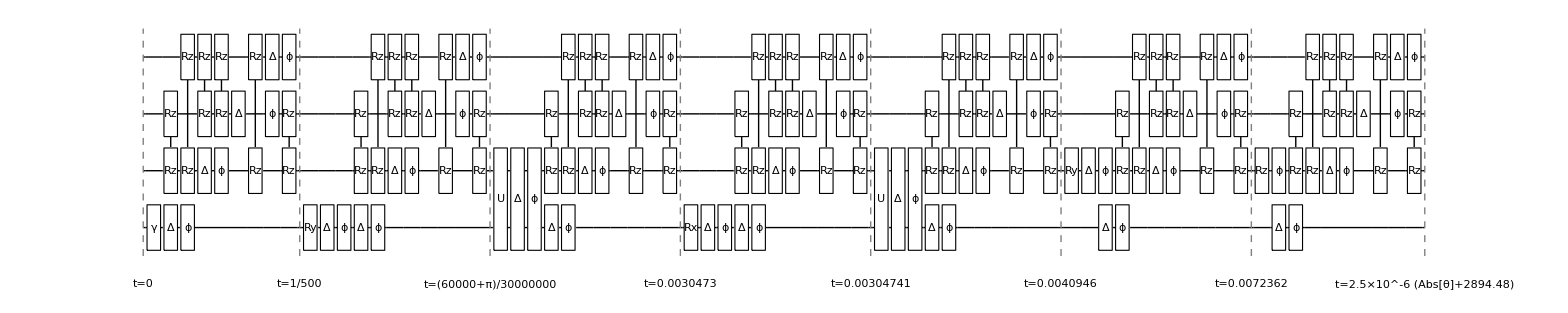

```mathematica
nuprepNoisy=Assuming[Element[θ,Reals],Simplify@InsertCircuitNoise[nuprep,NVDevice,ReplaceAliases->True]];
DrawCircuit@%
```

```mathematica
durprep=First@Last@nuprepNoisy/.θ->π
```

0.00724405

```mathematica
(* Start with a complete mixed state for consistent result *)
ρinit=IdentityMatrix[2^4]/2^4;
resPrepNuclear=Table[
param=j π/4;
noisycirc=ExtractCircuit[ nuprepNoisy/.θ->param];
(* Cross check, if superoperate operates the same way as QuEST *)
SetQuregMatrix[ρ4,ρinit];
ApplyCircuit[ρ4,noisycirc];
ρetom=PartialTrace[GetQuregState@ρ4,0,2,3];
ρeid=xyDensityMatrix[param];
{param, CalcFidelityDensityMatrices[ρetom,ρeid],ρetom,ρeid}
,{j,0,7}];
```

```mathematica
Grid[{#[[1]],#[[2]],TraditionalForm@Chop@#[[3]],TraditionalForm@Chop@N@#[[4]]}&/@resPrepNuclear]
```

0 | 0.983547 | (0.5 | 0.483547
0.483547 | 0.5) | (0.5 | 0.5
0.5 | 0.5)
π/4 | 0.98351 | (0.5 | 0.341893-0.341893 ⅈ
0.341893+0.341893 ⅈ | 0.5) | (0.5 | 0.353553-0.353553 ⅈ
0.353553+0.353553 ⅈ | 0.5)
π/2 | 0.983474 | (0.5 | 0.-0.483474 ⅈ
0.+0.483474 ⅈ | 0.5) | (0.5 | 0.-0.5 ⅈ
0.+0.5 ⅈ | 0.5)
(3 π)/4 | 0.983438 | (0.5 | -0.341842-0.341842 ⅈ
-0.341842+0.341842 ⅈ | 0.5) | (0.5 | -0.353553-0.353553 ⅈ
-0.353553+0.353553 ⅈ | 0.5)
π | 0.983402 | (0.5 | -0.483402
-0.483402 | 0.5) | (0.5 | -0.5
-0.5 | 0.5)
(5 π)/4 | 0.983365 | (0.5 | -0.341791+0.341791 ⅈ
-0.341791-0.341791 ⅈ | 0.5) | (0.5 | -0.353553+0.353553 ⅈ
-0.353553-0.353553 ⅈ | 0.5)
(3 π)/2 | 0.983329 | (0.5 | 0.+0.483329 ⅈ
0.-0.483329 ⅈ | 0.5) | (0.5 | 0.+0.5 ⅈ
0.-0.5 ⅈ | 0.5)
(7 π)/4 | 0.983293 | (0.5 | 0.34174+0.34174 ⅈ
0.34174-0.34174 ⅈ | 0.5) | (0.5 | 0.353553+0.353553 ⅈ
0.353553-0.353553 ⅈ | 0.5)

## GRAPHIX noise extraction: nuclear spin preparation

```mathematica
ChoiToKraus::usage="Transform Choi matrix to Kraus map form.";
ChoiToKraus[choi_]:=With[{kraus = Sqrt[#[[1]]]*Tensorize[#[[2]]]& /@ (Transpose @ Eigensystem[choi])},
	Assert[Chop@Total[#.ConjugateTranspose[#]& /@ kraus] === IdentityMatrix[Length@kraus[[1]]], "Kraus decomposition failed to be complete."];
	kraus
]
```

```mathematica
goalPrep=resPrepNuclear[[2]]
```

{π/4,0.98351,{{0.5+1.38778×10^-17 ⅈ,0.341893-0.341893 ⅈ},{0.341893+0.341893 ⅈ,0.5-1.38778×10^-17 ⅈ}},{{1/2,1/2 ⅇ^(-(ⅈ π)/4)},{1/2 ⅇ^((ⅈ π)/4),1/2}}}

```mathematica
nuprep={Subscript[xyNuclear, 1][θ]}
```

{Init_0,Ry_0[π/2],CRx_(0,1)[π/2],Rx_0[π/2],CRy_(0,1)[-π/2],Ry_1[π/2],Rz_1[θ]}

1) Remove passive noise: cross-talk and exponential decay will disappear

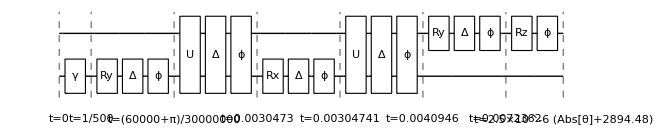

```mathematica
nuprepNoisy=Assuming[Element[θ,Reals],Simplify@InsertCircuitNoise[nuprep,NVCenterDelft[FreqWeakZZ->False,StdPassiveNoise->False],ReplaceAliases->True]];
DrawCircuit@%
```

```mathematica
ρ2=CreateDensityQureg[2];
```

```mathematica
param=π/4; (* pick one parameter *)
ρinit=IdentityMatrix[2^2]/2^2; (* maximally mixed state *)
noisycirc=ExtractCircuit[nuprepNoisy/.θ->param];
SetQuregMatrix[ρ2,ρinit];
ApplyCircuit[ρ2,noisycirc];
ρetom=PartialTrace[GetQuregState@ρ2,0];
ρeid=xyDensityMatrix[param];
resPrep={param, CalcFidelityDensityMatrices[ρetom,ρeid],Chop@ρetom,N@ρeid}
```

{π/4,0.983511,{{0.5,0.341894-0.341894 ⅈ},{0.341894+0.341894 ⅈ,0.5}},{{0.5,0.353553-0.353553 ⅈ},{0.353553+0.353553 ⅈ,0.5}}}

```mathematica
Norm/@(goalPrep-resPrep)
```

{0,7.91595×10^-7,7.91595×10^-7,0.}

```mathematica
MatrixForm@resPrep[[3]]
```

(0.5 | 0.341894-0.341894 ⅈ
0.341894+0.341894 ⅈ | 0.5)

```mathematica
ρideal=resPrep[[4]]
ρtomo=resPrep[[3]]
```

{{0.5,0.353553-0.353553 ⅈ},{0.353553+0.353553 ⅈ,0.5}}

{{0.5,0.341894-0.341894 ⅈ},{0.341894+0.341894 ⅈ,0.5}}

```mathematica
{choiop, elems,constrains,init}=hermitianTemplate[4,{d,a,b}];
```

```mathematica
xrpt2 =(TensorContract[ArrayReshape[choiop, {2, 2, 2, 2}], {2, 4}] == IdentityMatrix[2]);
cost = Simplify[ExpandAll@Norm[ChoiApply[ρideal, choiop]-ρtomo,"Frobenius"],elems];
 sol = ConvexOptimization[cost,{VectorGreaterEqual[{choiop, 0}, {"SemidefiniteCone", 4}],xrpt2},
elems, PerformanceGoal-> "Quality"];
```

```mathematica
MatrixForm@ChoiApply[ρideal,choiop/.sol]
MatrixForm@ρtomo
Norm[Chop@ChoiApply[ρideal,choiop/.sol]-ρtomo]
```

(0.5+0. ⅈ | 0.341894-0.341894 ⅈ
0.341894+0.341894 ⅈ | 0.5+0. ⅈ)

(0.5 | 0.341894-0.341894 ⅈ
0.341894+0.341894 ⅈ | 0.5)

2.12015×10^-11

```mathematica
Chop@MatrixForm[choiop/.sol]
```

(0.5 | 0 | 0 | 0.483511
0 | 0.5 | 0.-0.483511 ⅈ | 0
0 | 0.+0.483511 ⅈ | 0.5 | 0
0.483511 | 0 | 0 | 0.5)

```mathematica
kraus=ChoiToKraus[choiop/.sol];
(* test*)
MatrixForm@Norm[Total[#.ρideal.ConjugateTranspose[#]&/@%]-ρtomo,1]
```

2.12017×10^-11

```mathematica
(* Test if this theta dependent is good approximation *)
Table[
param=j π/4;
ρideal=xyDensityMatrix[param];
ρnoisy=Total[#.ρideal.ConjugateTranspose[#]&/@kraus];
CalcFidelityDensityMatrices[ρideal,ρnoisy]
,{j,0,7 }]
```

{0.741756,0.983511,0.741756,0.5,0.741756,0.983511,0.741756,0.5}

Final gate noise

```mathematica
ngPrep = Table[
	param = j π/4;
	noisycirc=ExtractCircuit[nuprepNoisy/.θ->param];
	SetQuregMatrix[ρ2, IdentityMatrix[2^2]/2^2]; (* maximally mixed state *)
	ApplyCircuit[ρ2, noisycirc];
	ρtomo=Chop@PartialTrace[GetQuregState@ρ2, 0];
	ρideal=N@xyDensityMatrix[param];
	{choiop, elems,constrains,init} = hermitianTemplate[4, {d,a,b}];
	xrpt2 =(TensorContract[ArrayReshape[choiop, {2, 2, 2, 2}], {2, 4}] == IdentityMatrix[2]);
	cost = Simplify[ExpandAll@Norm[ChoiApply[ρideal, choiop]-ρtomo,"Frobenius"], elems];
	sol = ConvexOptimization[cost,{VectorGreaterEqual[{choiop, 0}, {"SemidefiniteCone", 4}],xrpt2}, elems, PerformanceGoal-> "Quality"];
	kraus = ChoiToKraus[choiop/.sol];
	(* test*)
	Print@{param, Norm[Total[#.ρideal.ConjugateTranspose[#]&/@kraus]-ρtomo,1], CalcFidelityDensityMatrices[ρtomo, ρideal]};
	ToString[j] -> {Chop @ Re @ kraus, Chop @ Im @ kraus}
,{j,0,7}];
```

{0,2.70243×10^-11,0.983547}

{π/4,2.12017×10^-11,0.983511}

{π/2,2.13052×10^-11,0.983475}

{(3 π)/4,2.10566×10^-11,0.983439}

{π,2.04316×10^-11,0.983402}

{(5 π)/4,2.13913×10^-11,0.983366}

{(3 π)/2,2.19755×10^-11,0.98333}

{(7 π)/4,2.21855×10^-11,0.983294}

```mathematica
NVNoise["ngPrep"]=ngPrep;
```

```mathematica
NVNoise["durPrep"]=Table[ToString[j] -> First@Last@nuprepNoisy/.θ->j π/4 , {j, 0, 7}]
```

{0→0.0072362,1→0.00723816,2→0.00724012,3→0.00724209,4→0.00724405,5→0.00724601,6→0.00724798,7→0.00724994}

```mathematica
kraus[[2]]
```

{{0.689251-2.71866×10^-12 ⅈ,0.0741073-0.105297 ⅈ},{-0.105297-0.0741073 ⅈ,0.689251+0. ⅈ}}

```mathematica
kraus[[1]]+ⅈ kraus[[2]]
```

{{0.128761+0.689251 ⅈ,-0.291397+0.637758 ⅈ},{0.637758+0.291397 ⅈ,0.128761+0.689251 ⅈ}}

```mathematica
ngPrep[[1]][[2]][[1]]
```

{{{-0.0790696,-0.696794},{-0.696794,-0.0790696}},{{0.696794,-0.0790696},{-0.0790696,0.696794}},{{0.0642464,0.0640208},{-0.0640208,-0.0642464}},{{-0.0640208,0.0642464},{-0.0642464,0.0640208}}}

```mathematica
Table[
ρideal=N@xyDensityMatrix[j π/4];
kraus=ngPrep[[j+1]][[2]];
kmap=kraus[[1]]+ⅈ kraus[[2]];
ρtomo=Total[#.ρideal.ConjugateTranspose[#]&/@ kmap];
CalcFidelityDensityMatrices[ρideal,ρtomo]
,{j, 0,7}]
```

{0.983547,0.983511,0.983475,0.983439,0.983402,0.983366,0.98333,0.983294}

## CZ operations

## CZ operation between electron-nuclear spin

```mathematica
Subscript[CZen, q_/;q>0] := Sequence @@ {Subscript[Init, 0],Subscript[Rx, q][π/2], Subscript[CRy, 0,q][-π/2], Subscript[Rz, 0][-π/2], Subscript[Ry, q][π/2], Subscript[Rx, q][-π/2]}
```

```mathematica
MatrixForm[ ⅇ^(-ⅈ  π/4)CalcCircuitMatrix@Flatten[{Subscript[CZen, 1]}/.NVDevice[Aliases]]]
```

(0.707107-0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107-0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.707107-0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107-0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107-0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107-0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107-0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107-0.707107 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

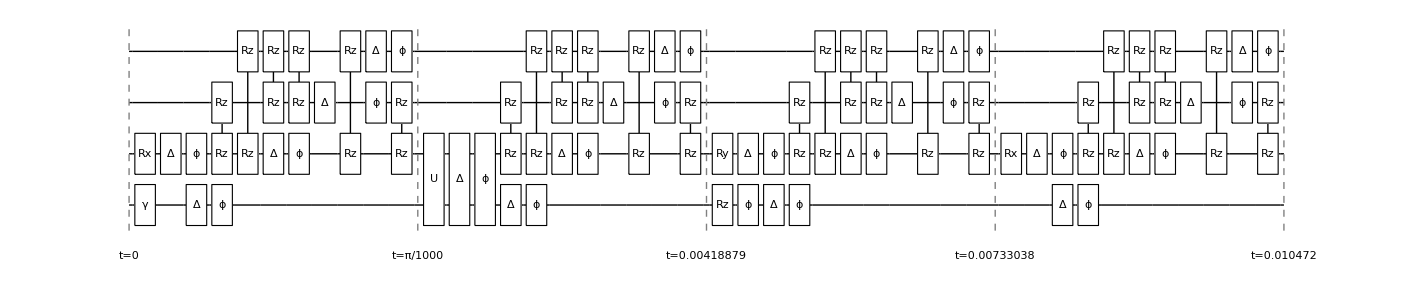

```mathematica
noisycze=InsertCircuitNoise[{Subscript[CZen, 1]}, NVDevice,ReplaceAliases->True];
DrawCircuit@%
```

## CZ operation between nuclear - nuclear spin

CZ operation between nuclear-nuclear spins uses the following tricks:
SWAP the state of nuclear spin to the electron spin , CZe, SWAP again

```mathematica
Subscript[CXen, q_/;q>0]:=Sequence @@ {Subscript[CRx, 0,q][π/2],Subscript[Rz, 0][-π/2],Subscript[Rx, q][-π/2]};
Subscript[SWAPen, q_/;q>0]:=Sequence@@{Subscript[CXen, q],Subscript[Ry, 0][-π/2],Subscript[Rz, 0][π],Subscript[Ry, q][-π/2],Subscript[Rz, q][π],Subscript[CXen, q],Subscript[Ry, 0][-π/2],Subscript[Rz, 0][π],Subscript[Ry, q][-π/2],Subscript[Rz, q][π],Subscript[CXen, q]};
Subscript[CZnn, q1_/;q1>0,q2_/;q2>0]:=Sequence@@{Subscript[SWAPen, q1],Subscript[CZen, q2],Subscript[SWAPen, q1]}
```

```mathematica
(* Check if the SWAP works *)
MatrixForm[ⅇ^(-ⅈ 3π/4)CalcCircuitMatrix@Flatten[{Subscript[SWAPen, 1]}/.NVDevice[Aliases]]]
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(* Check if CZ between two-nuclear spins works *)
MatrixForm@ExpandAll[(ⅇ^((ⅈ π)/4)/4+ⅈ ⅇ^((-ⅈ π)/4)/4)*PartialTrace[CalcCircuitMatrix@Flatten[{Subscript[CZnn, 1,2]}/.NVDevice[Aliases]],0]]
```

(0.707107+0.707107 ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.49802×10^-33-1.49802×10^-33 ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.707107+0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 1.49802×10^-33-1.49802×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.707107+0.707107 ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.49802×10^-33-1.49802×10^-33 ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.707107+0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 1.49802×10^-33-1.49802×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
1.63421×10^-33-1.63421×10^-33 ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107+0.707107 ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 1.63421×10^-33-1.63421×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.707107+0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 1.63421×10^-33-1.63421×10^-33 ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107+0.707107 ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 1.63421×10^-33-1.63421×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.707107+0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107+0.707107 ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.49802×10^-33-1.49802×10^-33 ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.707107+0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 1.49802×10^-33-1.49802×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107+0.707107 ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.49802×10^-33-1.49802×10^-33 ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.707107+0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 1.49802×10^-33-1.49802×10^-33 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.63421×10^-33-1.63421×10^-33 ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107+0.707107 ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 1.63421×10^-33-1.63421×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.707107+0.707107 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.63421×10^-33-1.63421×10^-33 ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.707107+0.707107 ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -6.30628×10^-17+5.46941×10^-17 ⅈ | 1.63421×10^-33-1.63421×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.1359×10^-17+1.1359×10^-17 ⅈ | 0.707107+0.707107 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

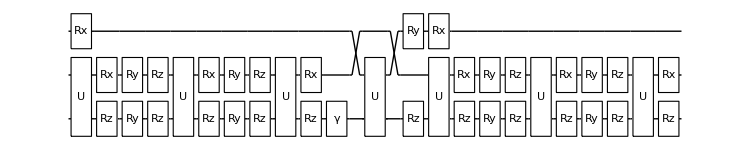

```mathematica
(* This looks overkill!!! :( *)
DrawCircuit@Flatten[{Subscript[CZnn, 1,2]}/.NVDevice[Aliases]]
```

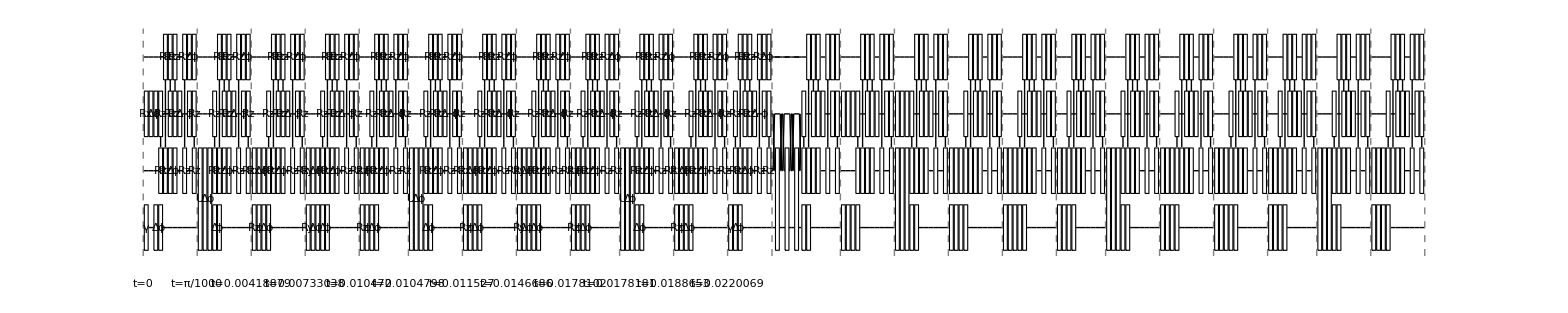

```mathematica
noisycznn=InsertCircuitNoise[{Subscript[Init, 0],Subscript[CZnn, 1,2]}, NVDevice,ReplaceAliases->True];
DrawCircuit@%
```

## GRAPHIX noise extraction:noisy CZ-operation

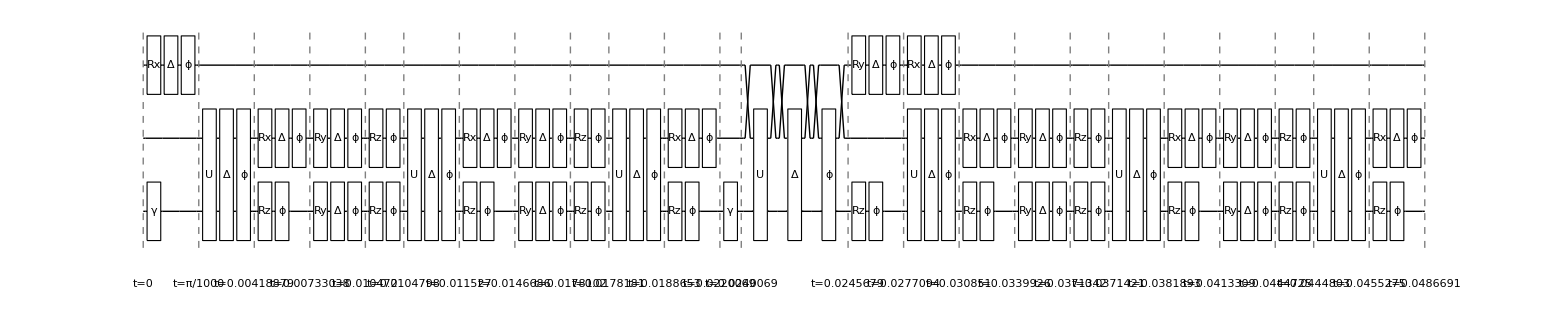

```mathematica
noisycznn=InsertCircuitNoise[{Subscript[Init, 0],Subscript[CZnn, 1,2]}, NVCenterDelft[StdPassiveNoise->False, FreqWeakZZ->False],ReplaceAliases->True];
DrawCircuit@%
```

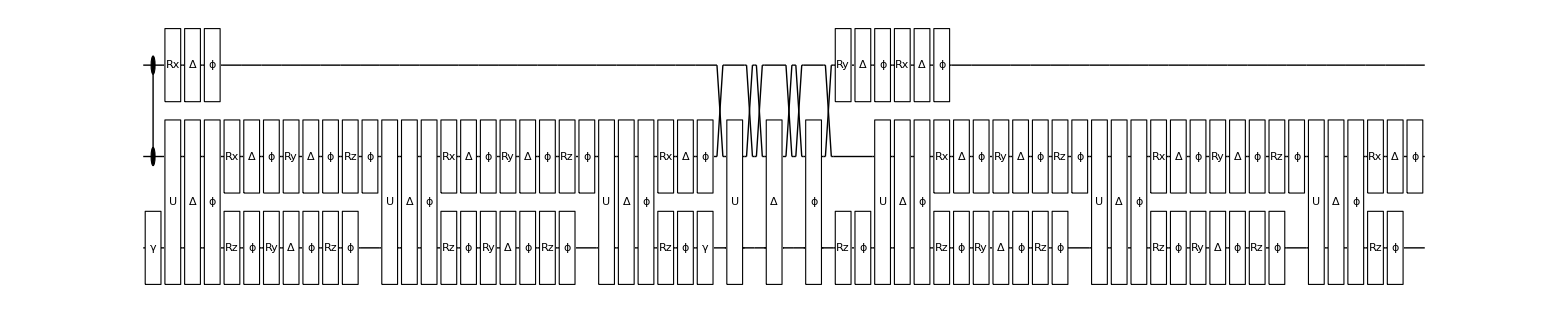

```mathematica
noisecz=Flatten@{Subscript[C, 1][Subscript[Z, 2]],ExtractCircuit[noisycznn]};
DrawCircuit@%
```

```mathematica
superopnoisecz=CalcCircuitMatrix[noisecz];
krausnoisecz=Chop@ChoiToKraus@RowShuffle@superopnoisecz;
```

```mathematica
NVNoise["ngCZ"]={Re@krausnoisecz,Im@krausnoisecz};
```

```mathematica
(* Test the result *)
noisycz1=CalcCircuitMatrix@ExtractCircuit@noisycznn;
```

```mathematica
(* Kraus map of extracted noise to ideal CZ *)
noisycz2=#.CalcCircuitMatrix[Subscript[C, 1][Subscript[Z, 2]]]& /@ krausnoisecz;
```

```mathematica
(* Calculate superoperator from the given kraus maps *)
superopcz2=Total[KroneckerProduct[Conjugate@#,#]& /@ noisycz2];
```

```mathematica
Norm[superopcz2-noisycz1]
```

3.28419×10^-15

```mathematica
NVNoise["durCZ"]=First@Last@noisycznn;
```

## Measurement

```mathematica
(*measurement sequences on nuclear spins the computational basis *)
Subscript[measZ, q_ /; q>0] := Sequence[Subscript[Ry, 0][π/2],Subscript[Rx, q][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Rx, 0][π/2],Subscript[M, 0]]
(*measurement sequences on nuclear spins the XY basis *)
Subscript[measXY, q_ /; q>0][θ_] := Sequence[Subscript[Init, 0], Subscript[Rz, q][-θ],Subscript[Ry, q][-π/2],Subscript[Ry, 0][π/2],Subscript[Rx, q][π/2],Subscript[CRy, 0,q][-π/2], Subscript[Rx, 0][π/2], Subscript[M, 0]]
```

{Damp_0[1.],Rz_1[-θ],Ry_1[-π/2],Ry_0[π/2],Rx_1[π/2],U_(0,1)[{{1/(√2),0,1/(√2),0},{0,1/(√2),0,-1/(√2)},{-1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)}}],Rx_0[π/2],M_0}

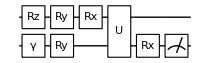

```mathematica
measxycirc=Flatten[{Subscript[measXY, 1][θ]}/. NVDevice[Aliases]]
DrawCircuit@%
```

```mathematica
ρ2=CreateDensityQureg[2];
```

```mathematica
(* test the circuit *)
Table[
parammeas=param+π;
(* set initial state as the perfect state and maximally mixed on electron *)
initρ=KroneckerProduct[xyDensityMatrix[param],{{0.5,0},{0,0.5}}];
Flatten@Table[
SetQuregMatrix[ρ2,initρ];
ApplyCircuit[ρ2,measxycirc/.θ->parammeas],
50],
{param, {0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4}}]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

## GRAPHIX noise extraction: measurement in XY basis on nuclear spin

```mathematica
(* perfect preparatio to inverse measurement *)
Subscript[prepXY, q_][θ_]:={Subscript[Ry, q][π/2],Subscript[Rz, q][θ]}
```

{{0,{Damp_0[0.999],Rz_1[-θ],Deph_1[Min[0.5,0.0000477465 Abs[θ]]]},{}},{Max[1/500,Abs[θ]/400000],{Ry_1[-π/2],Depol_1[0.00281779],Deph_1[0.000939264],Ry_0[π/2],Depol_0[0.000281303],Deph_0[0.0000937676]},{}},{π/1000+Max[1/500,Abs[θ]/400000],{Rx_1[π/2],Depol_1[0.00281779],Deph_1[0.000939264]},{}},{π/500+Max[1/500,Abs[θ]/400000],{U_(0,1)[{{1/(√2),0,1/(√2),0},{0,1/(√2),0,-1/(√2)},{-1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)}}],Depol_(0,1)[0.0112771],Deph_(0,1)[0.00125301]},{}},{0.00733038+Max[1/500,Abs[θ]/400000],{Rx_0[π/2],Depol_0[0.000281303],Deph_0[0.0000937676]},{}},{0.00733049+Max[1/500,Abs[θ]/400000],{X_0,Damp_0[0.054],X_0,M_0},{}},{0.00735049+Max[1/500,Abs[θ]/400000],{},{}}}

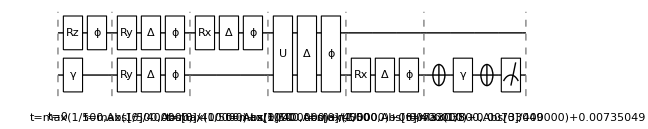

```mathematica
noisymeasurement=InsertCircuitNoise[{Subscript[measXY, 1][θ]},NVCenterDelft[FreqWeakZZ->False,StdPassiveNoise->False],ReplaceAliases->True]
DrawCircuit@%
```

```mathematica
NVNoise["durRead"]=Table[First@Last@noisymeasurement/.θ->j π/4,{j,0,7}]
```

{0.00935049,0.00935049,0.00935049,0.00935049,0.00935049,0.00935049,0.00935049,0.00935049}

```mathematica
(* test the circuit: FIDELITY of measurement is around 0.934, without decay and cross-talk :O  *)
(* set initial state as the perfect state and maximally mixed on electron *)
initρ=KroneckerProduct[xyDensityMatrix[π],{{0.5,0},{0,0.5}}];
circ=DeleteCases[ExtractCircuit@noisymeasurement,Subscript[M, _]];
SetQuregMatrix[ρ2,initρ];
ApplyCircuit[ρ2,circ];
ρ2mat=GetQuregState[ρ2];
Re[ρ2mat[[1,1]]+ρ2mat[[3,3]]]
```

ApplyCircuit::error: Circuit contains non-numerical or non-real parameters!

0.5

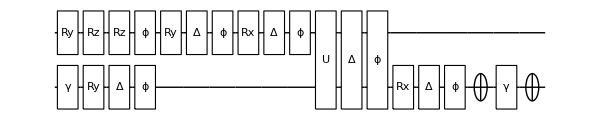

```mathematica
(* measinv o noisymeas = efffective noise on measurement*)
noiseonmeasure=Join[Subscript[prepXY, 1][θ],DeleteCases[ExtractCircuit@noisymeasurement,Subscript[M, _]]];
DrawCircuit@%
```

```mathematica
(* Check performance of the approximated measurement:   noise o meas  *)
ngRead=Table[
param={θ->j π/4};
circ=Join[{Subscript[Rz, 1][-θ],Subscript[Ry, 1][-π/2]}/.param,noiseonmeasure/.param];
initρ=KroneckerProduct[xyDensityMatrix[θ/.param],{{0.5,0},{0,0.5}}];
SetQuregMatrix[ρ2,initρ];
ApplyCircuit[ρ2,circ];
ρ2mat=GetQuregState[ρ2];
Print@Re[ρ2mat[[1,1]]+ρ2mat[[3,3]]];
superopmeas=CalcCircuitMatrix[noiseonmeasure/.param];
 krausmeas=Chop@ChoiToKraus@RowShuffle@superopmeas;
ToString[j]->{Re@krausmeas,Im@krausmeas}
,{j,0,7}];
```

0.934266

0.934231

0.934197

0.934162

0.934127

0.934093

0.934058

0.934024

```mathematica
NVNoise["ngRead"]=ngRead;
```

```mathematica
config=Association@Options@NVCenterDelft
```

<|QubitNum→4,T1→<|0→3600,1→60,2→60,3→60|>,T2→<|0→1.5,1→10,2→10,3→10|>,FreqWeakZZ→5,FreqSingleXY→<|0→15000000,1→500,2→500,3→500|>,FreqSingleZ→<|0→32000000,1→400000,2→400000,3→400000|>,FreqCRot→<|1→1500.,2→2800.,3→800.|>,FidCRot→<|1→0.98,2→0.98,3→0.98|>,FidSingleXY→<|0→0.9995,1→0.995,2→0.995,3→0.99|>,FidSingleZ→<|0→0.9999,1→0.9999,2→0.99999,3→0.9999|>,EFSingleXY→{0.75,0.25},EFCRot→{0.9,0.1},FidInit→0.999,DurInit→1/500,FidMeas→0.946,DurMeas→1/50000,StdPassiveNoise→True|>

```mathematica
NVNoise["T1"]=List@@config[T1];
NVNoise["T2"]=List@@config[T2];
NVNoise["crosstalk"]=config[FreqWeakZZ];
```

```mathematica
Keys@NVNoise
```

{description,ngPrep,durPrep,ngCZ,durCZ,durRead,ngRead,T1,T2,crosstalk}

```mathematica
Export["NVNoise.json",Normal@NVNoise]
```

NVNoise.json

```mathematica
Dimensions/@NVNoise["ngRead"]
```

{{2},{2},{2},{2},{2},{2},{2},{2}}